```mathematica
Aproksimiraj[n_] := Module[{R},
g1 = Graphics[{Blue,Opacity[.5], Polygon[Table[{Cos[2π/n*k], Sin[2π/n*k]}, {k, 0, n-1}]]}];
R = Sqrt[1 + Tan[π/n]^2];
g2 = Graphics[{Blue,Opacity[.2], Polygon[Table[{R*Cos[π/n*(2*k+1)], R*Sin[π/n*(2*k+1)]}, {k, 0, n-1}]]}];
g3 = Graphics[Circle[{0, 0}, 1]];
Show[{g2, g1, g3}]
]
```

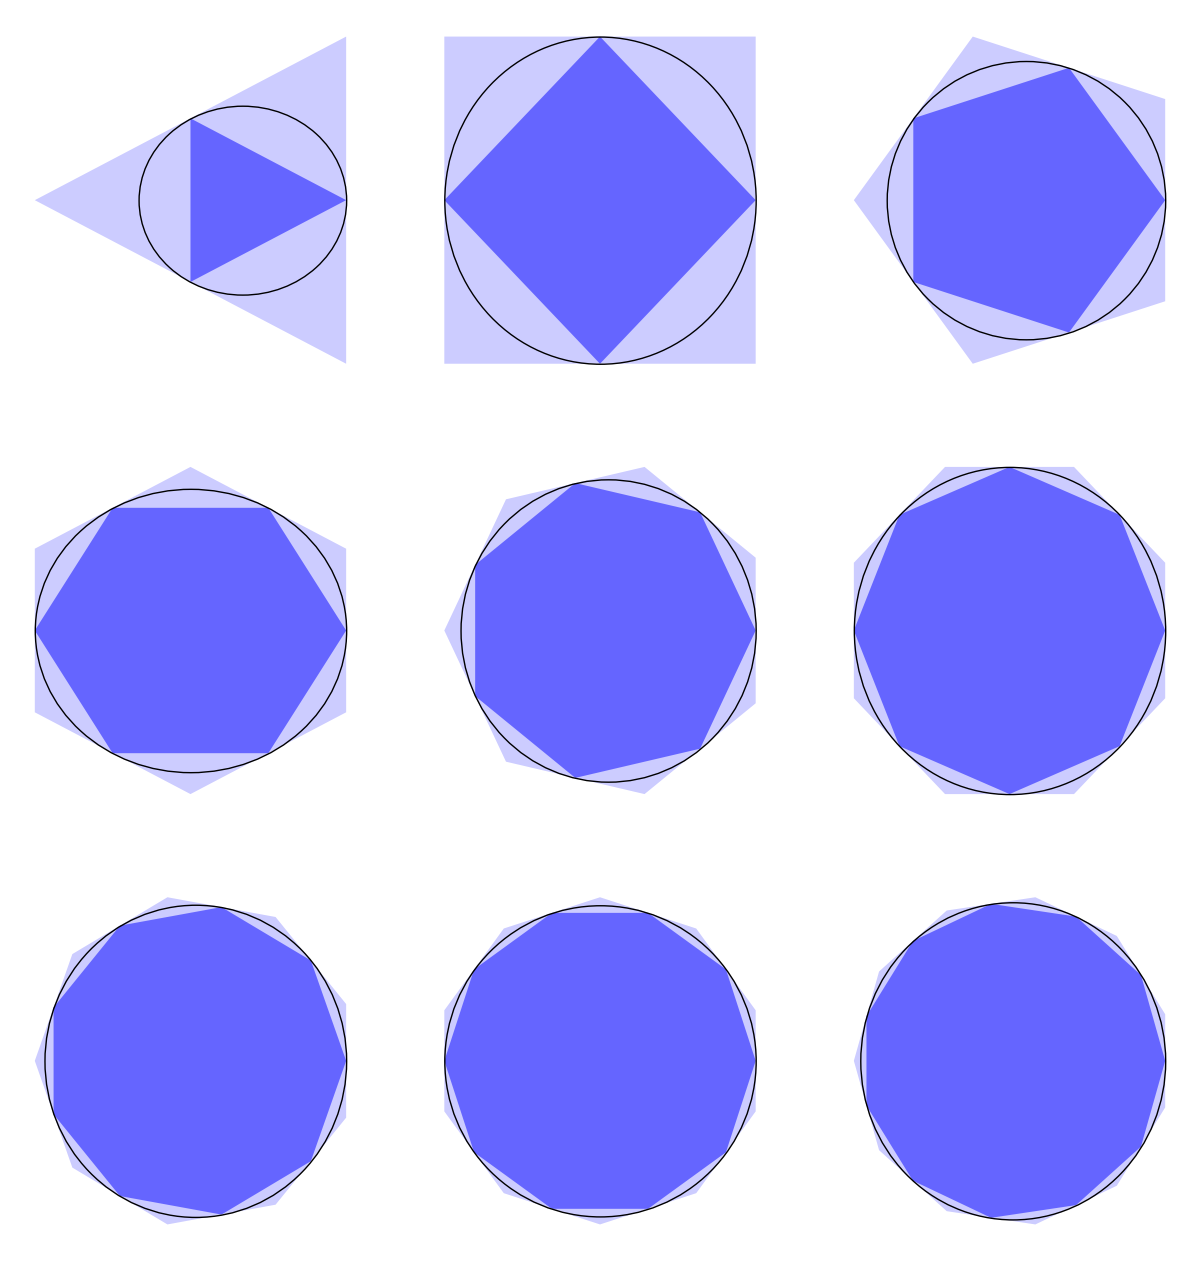

```mathematica
GraphicsGrid[
Partition[Table[Aproksimiraj[n],
{n, 3, 11}], 3]]
```

```mathematica
Export["poligoni.eps", %]
```

poligoni.eps